```mathematica
Inverse[ⅈ ω PauliMatrix[0]-vf kx PauliMatrix[1]-vf ky PauliMatrix[2]]
```

{{(ⅈ ω)/(-kx^2 vf^2-ky^2 vf^2-ω^2),(kx vf-ⅈ ky vf)/(-kx^2 vf^2-ky^2 vf^2-ω^2)},{(kx vf+ⅈ ky vf)/(-kx^2 vf^2-ky^2 vf^2-ω^2),(ⅈ ω)/(-kx^2 vf^2-ky^2 vf^2-ω^2)}}

```mathematica
Integrate[{{(ⅈ ω)/(-kx^2 vf^2-ky^2 vf^2-ω^2),(kx vf)/(-kx^2 vf^2-ky^2 vf^2-ω^2)},{(kx vf)/(-kx^2 vf^2-ky^2 vf^2-ω^2),(ⅈ ω)/(-kx^2 vf^2-ky^2 vf^2-ω^2)}},{ky,-∞,∞},GenerateConditions->False]
```

{{-(ⅈ π ω √(vf^2/(kx^2 vf^2+ω^2)))/vf^2,-(kx π √(vf^2/(kx^2 vf^2+ω^2)))/vf},{-(kx π √(vf^2/(kx^2 vf^2+ω^2)))/vf,-(ⅈ π ω √(vf^2/(kx^2 vf^2+ω^2)))/vf^2}}

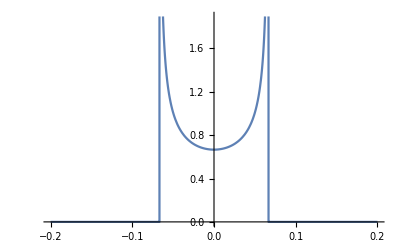

```mathematica
Plot[Im[(ω √(vf^2/(kx^2 vf^2-ω^2)))/vf^2]/.{vf->3/2,ω->0.1},{kx,-0.2,0.2}]
```

```mathematica
Inverse[ⅈ ω PauliMatrix[0]-1/(2 m){{0,(kx-ⅈ ky)^2+v3(kx+ⅈ ky)},{(kx+ⅈ ky)^2+v3(kx-ⅈ ky),0}}]
```

{{(ⅈ ω)/(-(((kx+ⅈ ky)^2+(kx-ⅈ ky) v3) ((kx-ⅈ ky)^2+(kx+ⅈ ky) v3))/(4 m^2)-ω^2),((kx-ⅈ ky)^2+(kx+ⅈ ky) v3)/(2 m (-(((kx+ⅈ ky)^2+(kx-ⅈ ky) v3) ((kx-ⅈ ky)^2+(kx+ⅈ ky) v3))/(4 m^2)-ω^2))},{((kx+ⅈ ky)^2+(kx-ⅈ ky) v3)/(2 m (-(((kx+ⅈ ky)^2+(kx-ⅈ ky) v3) ((kx-ⅈ ky)^2+(kx+ⅈ ky) v3))/(4 m^2)-ω^2)),(ⅈ ω)/(-(((kx+ⅈ ky)^2+(kx-ⅈ ky) v3) ((kx-ⅈ ky)^2+(kx+ⅈ ky) v3))/(4 m^2)-ω^2)}}

```mathematica
Integrate[ω/(-(((kx+ⅈ ky)^2+(kx-ⅈ ky) v3) ((kx-ⅈ ky)^2+(kx+ⅈ ky) v3))/(4 m^2)+(ω+ⅈ δ)^2),{ky,-∞,∞},GenerateConditions->False]//FullSimplify
```

(4 m^2 π (-((-1)^Floor[(π+Arg[2 kx^2-6 kx v3+v3^2-√(-((8 kx-v3) v3 (-2 kx+v3)^2)-16 m^2 (δ-ⅈ ω)^2)])/(2 π)])/(√(2 kx^2-6 kx v3+v3^2-√(-((8 kx-v3) v3 (-2 kx+v3)^2)-16 m^2 (δ-ⅈ ω)^2)))+((-1)^Floor[(π+Arg[2 kx^2-6 kx v3+v3^2+√(-((8 kx-v3) v3 (-2 kx+v3)^2)-16 m^2 (δ-ⅈ ω)^2)])/(2 π)])/(√(2 kx^2-6 kx v3+v3^2+√(-((8 kx-v3) v3 (-2 kx+v3)^2)-16 m^2 (δ-ⅈ ω)^2)))) ω)/(√(-1/2 (8 kx-v3) v3 (-2 kx+v3)^2-8 m^2 (δ-ⅈ ω)^2))

```mathematica
m π (-√(1/(kx^2-2 ⅈm ω))+√(1/(kx^2+2 ⅈ m ω)))
```

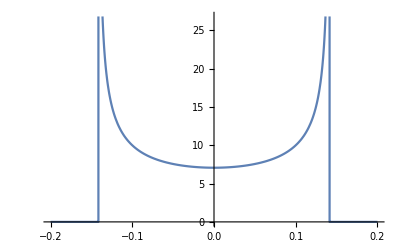

```mathematica
Plot[-Im[ (-√(1/(kx^2-2  ω))+√(1/(kx^2+2  ω)))]/.ω->0.01,{kx,-0.2,0.2}]
```

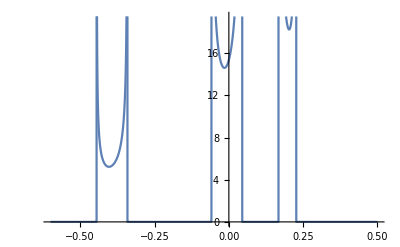

```mathematica
Plot[-Im[(4 m^2 π (-((-1)^Floor[(π+Arg[2 kx^2-6 kx v3+v3^2-√(-((8 kx-v3) v3 (-2 kx+v3)^2)-16 m^2 (δ-ⅈ ω)^2)])/(2 π)])/(√(2 kx^2-6 kx v3+v3^2-√(-((8 kx-v3) v3 (-2 kx+v3)^2)-16 m^2 (δ-ⅈ ω)^2)))+((-1)^Floor[(π+Arg[2 kx^2-6 kx v3+v3^2+√(-((8 kx-v3) v3 (-2 kx+v3)^2)-16 m^2 (δ-ⅈ ω)^2)])/(2 π)])/(√(2 kx^2-6 kx v3+v3^2+√(-((8 kx-v3) v3 (-2 kx+v3)^2)-16 m^2 (δ-ⅈ ω)^2)))) ω)/(√(-1/2 (8 kx-v3) v3 (-2 kx+v3)^2-8 m^2 (δ-ⅈ ω)^2))]/.{m->1,ω->0.01,δ->0.00000001,v3->0.4},{kx,-0.6,0.5}]
```